```mathematica
j[l_,x_]=Sqrt[Pi/(2*x)]*BesselJ[l +1/2, x]
```

√(π/2) √(1/x) BesselJ[1/2+l,x]

```mathematica
n[l_,x_]=Sqrt[Pi/(2*x)]*BesselY[l+1/2, x]
```

√(π/2) √(1/x) BesselY[1/2+l,x]

```mathematica
l = 2
```

2

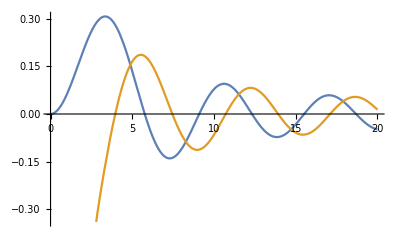

```mathematica
Plot[{j[l,x], n[l,x]}, {x, 0, 20}]
```

```mathematica
m=1
n=2
Integrate[j[m,x]*j[n,x], {x, -Infinity, Infinity}]
```

1

2

0